(2 (-1)^(1+n) Sin[n x])/n

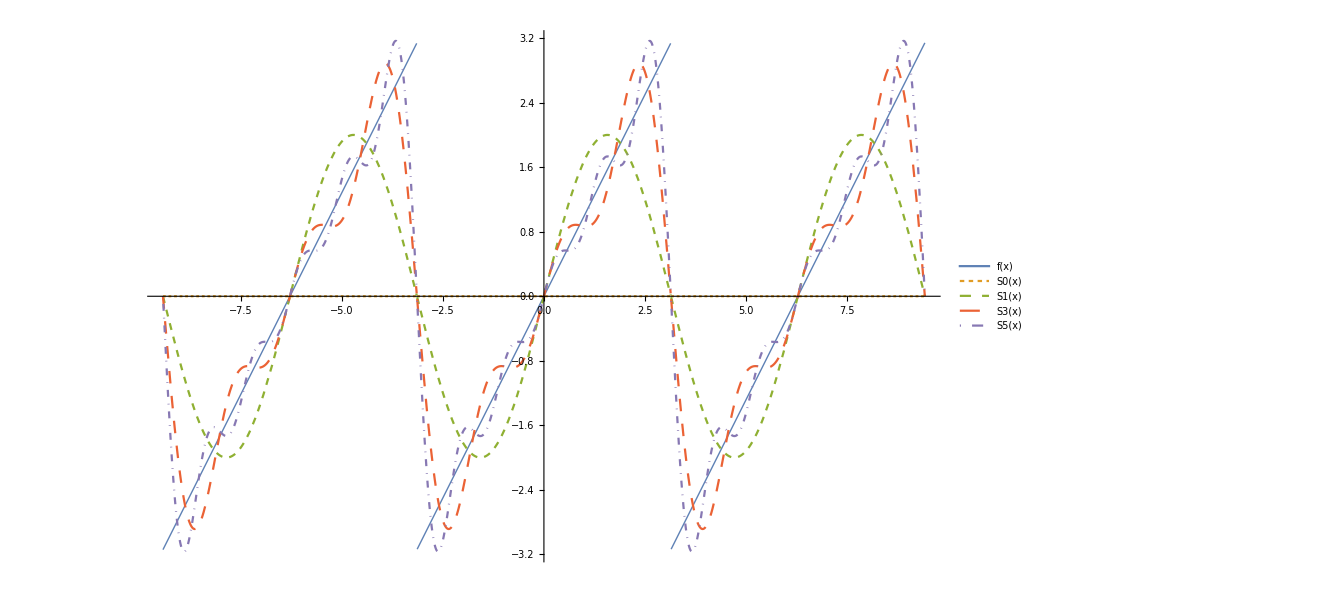

```mathematica
f = (2*Sin[n*x]*(-1)^(n + 1))/(n)
G[__x] := If[x< Pi, x, x - Pi]
Plot[{If[x <  - Pi, x + 2 * Pi, If[x > Pi, x -2*Pi, x]] ,0, Sum[f, {n, 1, 1}], Sum[f, {n, 1, 3}],Sum[f, {n, 1, 5}]}, {x, -3Pi , 3Pi }, PlotStyle->{ Thick, Dashing[Tiny], Dashing[Small], Dashing[Medium], DotDashed}, PlotLegends-> {"f(x)", "S0(x)","S1(x)","S3(x)","S5(x)" }]
```

```mathematica
Export["", Plot[{If[x <  - Pi, x + 2 * Pi, If[x > Pi, x -2*Pi, x]] ,0, Sum[f, {n, 1, 1}], Sum[f, {n, 1, 3}],Sum[f, {n, 1, 5}]}, {x, -3Pi , 3Pi }, PlotStyle->{ Thick, Dashing[Tiny], Dashing[Small], Dashing[Medium], DotDashed}, PlotLegends-> {"f(x)", "S0(x)","S1(x)","S3(x)","S5(x)" }]]
```

Export::chtype: First argument "" is not a valid file specification.

$Failed